```mathematica
(* https://mathematica.stackexchange.com/questions/261561/generating-1-f-noise *)
(* Timmer Konig 1995 *)
(* astrochron/R/FUNCTION-makeNoise_v3.R *)
```

```mathematica
nn=2^16 (*Number of spectral points*)
S[f_]:=1/f;
s1=Table[If[f!=nn/2,
(RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]]),
RandomVariate[NormalDistribution[]]]*
 Sqrt[S[f]/2],{f,1,nn/2 }];
s2=Join[{0},s1,Reverse[Conjugate[s1[[1;;-2]]]]];
pwr=s2.Conjugate[s2];
norm=1/Sqrt[pwr];
```

65536

{0.003869,Null}

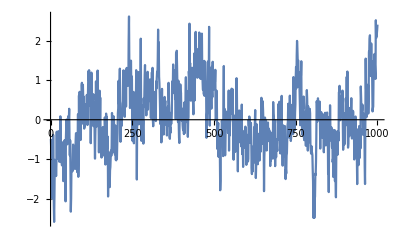

```mathematica
Timing[if=InverseFourier[s2,FourierParameters->{-1,-1}];]
l=Chop[norm if];
ListLinePlot[Take[l,UpTo[1000]]]
```

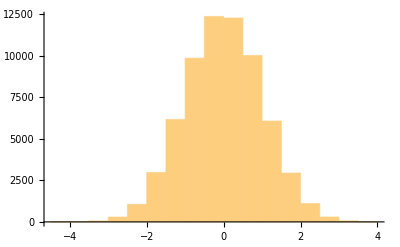

2.08167×10^-17

1.00001

```mathematica
Histogram[l]
avg=Mean[l]
std=StandardDeviation[l]
```

{{0,1.},{1,0.825449},{2,0.742116},{3,0.703345},{4,0.671023},{5,0.649116},{6,0.62795},{7,0.612634},{8,0.597198},{9,0.584225},{10,0.574054},{11,0.565799},{12,0.557865},{13,0.551686},{14,0.543453},{15,0.53807},{16,0.533143},{17,0.527612},{18,0.521653},{19,0.516724},{20,0.511028},{21,0.506227},{22,0.500922},{23,0.496994},{24,0.490792},{25,0.485021},{26,0.479615},{27,0.475937},{28,0.47039},{29,0.463184},{30,0.458421},{31,0.454106},{32,0.449472},{33,0.445097},{34,0.442407},{35,0.438944},{36,0.436037},{37,0.432668},{38,0.427245},{39,0.42448},{40,0.4209},{41,0.417431},{42,0.416224},{43,0.414072},{44,0.410659},{45,0.407816},{46,0.404535},{47,0.402337},{48,0.401237},{49,0.400178},{50,0.396773},{51,0.393223},{52,0.391067},{53,0.389343},{54,0.38706},{55,0.386168},{56,0.383389},{57,0.381},{58,0.379937},{59,0.377736},{60,0.375964},{61,0.37251},{62,0.369967},{63,0.367686},{64,0.365877},{65,0.363444},{66,0.36399},{67,0.362906},{68,0.361615},{69,0.358784},{70,0.356891},{71,0.354479},{72,0.352414},{73,0.350906},{74,0.348814},{75,0.348661},{76,0.348441},{77,0.346266},{78,0.345781},{79,0.346875},{80,0.343232},{81,0.342264},{82,0.341922},{83,0.337949},{84,0.33588},{85,0.335814},{86,0.335086},{87,0.33409},{88,0.331787},{89,0.329828},{90,0.32814},{91,0.32719},{92,0.328724},{93,0.328289},{94,0.326501},{95,0.324767},{96,0.322643},{97,0.319604},{98,0.317291},{99,0.317399},{100,0.316267}}

{a→0.834593,b→0.111836}

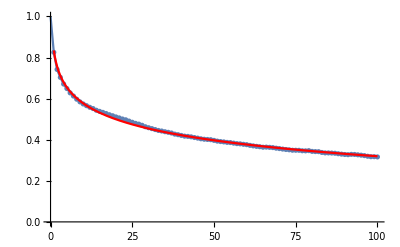

```mathematica
cf=Table[{i,CorrelationFunction[l-avg,i]},{i,0,100}]
p1=ListPlot[cf,PlotRange->{0,1},Joined->True,Mesh->All];
fnc=a-b Log[t];
sol=FindFit[Drop[cf,1],fnc,{a,b},t]
fnc=fnc/.sol;
p2=Plot[fnc,{t,1,100},PlotStyle->Red];
Show[p1,p2]
(* Logarithmic autocorrelation, see Kechner 1982 *)
```

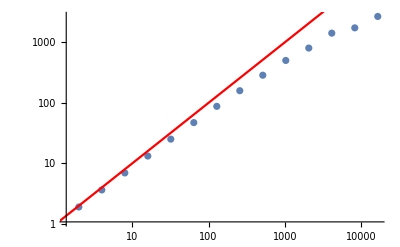

```mathematica
tab=Table[{2^i,StandardDeviation[Map[Total,Partition[l,2^i]]]},{i,14}];
p1=ListLogLogPlot[tab];
p2=LogLogPlot[{1x^(1)},{x,1,Length[l]},PlotStyle->{Red}];
Show[p1,p2]
```

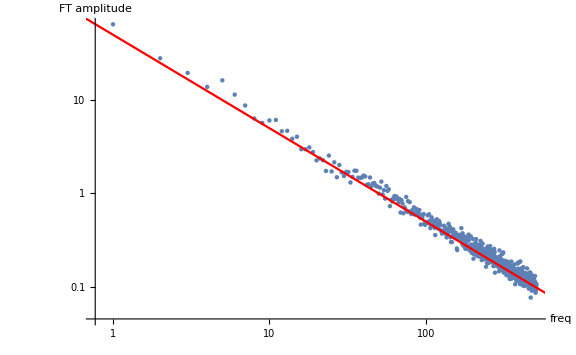

```mathematica
sz=1024;
pl=Partition[l,sz];
(* power spectrum ! *)
pl=Map[(μ=Mean[#];Rest[Take[Abs[Fourier[#-μ]]^2,sz/2]])&,pl];
plavg=Mean[pl];
pft1=ListLogLogPlot[plavg,PlotRange->All,AxesLabel->{"freq","FT amplitude"},LabelStyle->Larger];
pft2=LogLogPlot[{50/ω},{ω,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```